```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults.json"];
raw= Association[#]&/@raw;
```

```mathematica
raw[[1]]//Keys
```

{config,sigmaSet,cutSet,MTESet,solSet,norm_emit_x,norm_emit_y,emitSI90_x,emitSI90_y,sigmaSI90_x,sigmaSI90_y}

```mathematica
raw[[1]]
```

<|config→iris,sigmaSet→1.78,cutSet→2.67,MTESet→1,solSet→-0.38,norm_emit_x→8.4266×10^-6,norm_emit_y→8.4218×10^-6,emitSI90_x→7.6556×10^-6,emitSI90_y→7.8555×10^-6,sigmaSI90_x→0.00104031,sigmaSI90_y→0.00104061|>

```mathematica
groupedData = GroupBy[raw,#MTESet&];
```

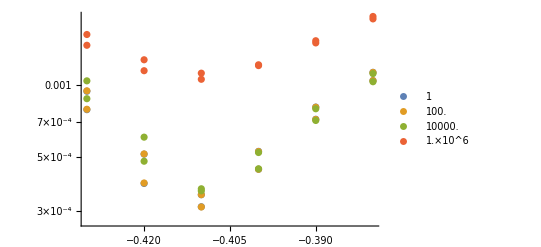

```mathematica
ListLogPlot[
Values[
{#["solSet"],#["sigmaSI90_x"]}&/@#&/@groupedData
],
PlotRange->All,
PlotLegends->Keys[groupedData]
]
```

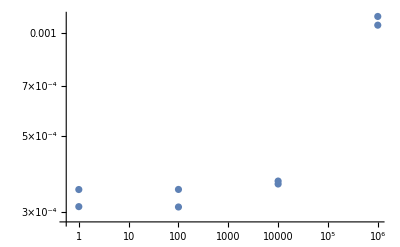

```mathematica
ListLogLogPlot[
{#MTESet,#["sigmaSI90_x"]}&/@Select[raw,#solSet == -0.41&]
]
```

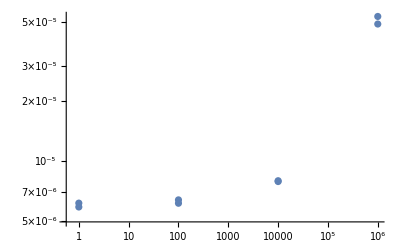

```mathematica
ListLogLogPlot[
{#MTESet,#["emitSI90_x"]}&/@Select[raw,#solSet == -0.41&]
]
```